```mathematica
ClearAll["Global`*"]
<<Utilities`CleanSlate`
CleanSlate[]
ClearInOut[]


pdConv[f_]:=TraditionalForm[f/.Derivative[inds__][g_][vars__]:>Apply[Defer[D[g[vars],##]]&,Transpose[{{vars},{inds}}]/.{{var_,0}:>Sequence[],{var_,1}:>{var}}]]

Needs["VariationalMethods`"]
```

(CleanSlate) Contexts purged: {Global`}

(CleanSlate) Approximate kernel memory recovered: 245 Kb

{Utilities`CleanSlate`,CompiledFunctionTools`,IPOPTLink`,VariationalMethods`,Parallel`Debug`Perfmon`,Parallel`Debug`,System`,Global`}

```mathematica
(* Work on making the intial conditions a bit more believable *)
```

```mathematica
Clear[ℒ]
ℒ = 
1/2 ℐ ( θ1'[t]^2 + θ2'[t]^2 ) - 1/2 k ( θ1[t]^2+ θ2[t]^2 + (θ1[t]- θ2[t])^2 ) ;
ℒ // pdConv
```

1/2 ℐ (((∂θ1(t))/(∂t))^2+((∂θ2(t))/(∂t))^2)-1/2 k ((θ1(t)-θ2(t))^2+(θ1(t))^2+(θ2(t))^2)

```mathematica
Clear[q]
q = { θ1[t] , θ2[t] } 
Clear[𝓆]
𝓆 = { η[t] , ξ[t] }
```

{θ1[t],θ2[t]}

{η[t],ξ[t]}

```mathematica
D[ D[ ℒ , D[q[[1]], t] ] , t ] - D[ ℒ , q[[1]] ] 
D[ D[ ℒ , D[q[[2]], t] ] , t ] - D[ ℒ , q[[2]] ]
```

1/2 k (2 θ1[t]+2 (θ1[t]-θ2[t]))+ℐ θ1''[t]

1/2 k (-2 (θ1[t]-θ2[t])+2 θ2[t])+ℐ θ2''[t]

```mathematica
Table[
D[ D[ ℒ , D[q[[i]], t] ] , t ] - D[ ℒ , q[[i]] ] == 0 ,
{ i , 1, 2 } ] // Expand  // Simplify  // TableForm
```

2 k θ1[t]+ℐ θ1''[t]==k θ2[t]
k θ1[t]==2 k θ2[t]+ℐ θ2''[t]

```mathematica
Clear[eqs]
eqs = 
EulerEquations[ ℒ , q , t ] ;
eqs // TableForm
```

-2 k θ1[t]+k θ2[t]-ℐ θ1''[t]==0
k θ1[t]-2 k θ2[t]-ℐ θ2''[t]==0

```mathematica
Clear[system]
system = { 
AddSides[ eqs[[1]] , eqs[[2]] ] // FullSimplify  , 
SubtractSides[ eqs[[1]] , eqs[[2]] ] // FullSimplify 
} ;
system // TableForm
```

k (θ1[t]+θ2[t])+ℐ (θ1''[t]+θ2''[t])==0
3 k θ1[t]+ℐ θ1''[t]==3 k θ2[t]+ℐ θ2''[t]

```mathematica
Clear[transform]
transform = { 
η[t] == θ1[t] + θ2[t] ,
ξ[t] == θ1[t] - θ2[t]
} ;
transform // TableForm
```

η[t]==θ1[t]+θ2[t]
ξ[t]==θ1[t]-θ2[t]

```mathematica
Clear[θ1θ2Replace]
θ1θ2Replace = 
Solve[ transform  , q ] // Flatten
```

{θ1[t]→1/2 (η[t]+ξ[t]),θ2[t]→1/2 (η[t]-ξ[t])}

```mathematica
Solve[ transform  , 𝓆 ] // Flatten
```

{η[t]→θ1[t]+θ2[t],ξ[t]→θ1[t]-θ2[t]}

```mathematica
Solve[ transform , q ] // Flatten
```

{θ1[t]→1/2 (η[t]+ξ[t]),θ2[t]→1/2 (η[t]-ξ[t])}

```mathematica
D[θ1θ2Replace, t]
D[D[θ1θ2Replace, t], t]
```

{θ1'[t]→1/2 (η'[t]+ξ'[t]),θ2'[t]→1/2 (η'[t]-ξ'[t])}

{θ1''[t]→1/2 (η''[t]+ξ''[t]),θ2''[t]→1/2 (η''[t]-ξ''[t])}

```mathematica
Clear[normal]
normal = 
system  /. θ1θ2Replace  /. D[D[θ1θ2Replace, t], t] // Expand  // Simplify   ;
normal // TableForm
```

k η[t]+ℐ η''[t]==0
3 k ξ[t]+ℐ ξ''[t]==0

```mathematica
transform /. t-> 0  /. θ1[0] -> 0 /. θ2[0]-> 0
```

{η[0]==0,ξ[0]==0}

```mathematica
D[transform, t]/. t-> 0  /. θ1'[0] -> 0 /. θ2'[0]-> 0
```

{η'[0]==0,ξ'[0]==0}

```mathematica
Clear[icsnormal]
icsnormal = 
Union[ transform /. t-> 0  /. θ1[0] -> 0 /. θ2[0]-> 0  , D[transform, t]/. t-> 0  /. θ1'[0] -> 0 /. θ2'[0]-> Ω ]
```

{η[0]==0,ξ[0]==0,η'[0]==Ω,ξ'[0]==-Ω}

```mathematica
normal
```

{k η[t]+ℐ η''[t]==0,3 k ξ[t]+ℐ ξ''[t]==0}

```mathematica
Union[ normal , icsnormal ]
```

{η[0]==0,ξ[0]==0,η'[0]==Ω,ξ'[0]==-Ω,k η[t]+ℐ η''[t]==0,3 k ξ[t]+ℐ ξ''[t]==0}

```mathematica
Clear[αβReplace]
αβReplace = 
Flatten[ DSolve[ Union[ normal , icsnormal ]  , 𝓆 , t ] ]
```

{η[t]→(√ℐ Ω Sin[(√k t)/(√ℐ)])/(√k),ξ[t]→-(√ℐ Ω Sin[(√3 √k t)/(√ℐ)])/(√3 √k)}

```mathematica
Flatten[ Solve[ transform , q ] ] 
Clear[θ1θ2solution]
θ1θ2solution = 
Flatten[ Solve[ transform , q ] ]  /. αβReplace
```

{θ1[t]→1/2 (η[t]+ξ[t]),θ2[t]→1/2 (η[t]-ξ[t])}

{θ1[t]→1/2 ((√ℐ Ω Sin[(√k t)/(√ℐ)])/(√k)-(√ℐ Ω Sin[(√3 √k t)/(√ℐ)])/(√3 √k)),θ2[t]→1/2 ((√ℐ Ω Sin[(√k t)/(√ℐ)])/(√k)+(√ℐ Ω Sin[(√3 √k t)/(√ℐ)])/(√3 √k))}

```mathematica
θ1θ2solution[[2]]
```

θ2[t]→1/2 ((√ℐ Ω Sin[(√k t)/(√ℐ)])/(√k)+(√ℐ Ω Sin[(√3 √k t)/(√ℐ)])/(√3 √k))

```mathematica
D[θ1θ2solution[[2]], t]
```

θ2'[t]→1/2 (Ω Cos[(√k t)/(√ℐ)]+Ω Cos[(√3 √k t)/(√ℐ)])

```mathematica
D[θ1θ2solution[[2,2]], t]
```

1/2 (Ω Cos[(√k t)/(√ℐ)]+Ω Cos[(√3 √k t)/(√ℐ)])

```mathematica
Solve[ D[θ1θ2solution[[2,2]], t] == 0  , t ]  /. C[1] -> 0
```

{{t→-((-1+√3) π √ℐ)/(2 √k)},{t→((1+√3) π √ℐ)/(2 √k)},{t→((-1+√3) π √ℐ)/(2 √k)},{t→-((1+√3) π √ℐ)/(2 √k)}}

```mathematica
Clear[parameters]
parameters = { 
k-> 10 , 
ℐ -> 40 
} ;
parameters // TableForm
```

k→10
ℐ→40

```mathematica
eqs /. parameters // Expand // TableForm
```

-20 θ1[t]+10 θ2[t]-40 θ1''[t]==0
10 θ1[t]-20 θ2[t]-40 θ2''[t]==0

```mathematica
Clear[ics]
ics = { 
θ1[0] == 0.1 ,
θ1'[0] == 0 ,
θ2[0] ==-  0.1 ,
θ2'[0] == 0
} ;
ics // TableForm
```

θ1[0]==0.1
θ1'[0]==0
θ2[0]==-0.1
θ2'[0]==0

```mathematica
Clear[solution]
solution[t_] = 
First[NDSolve[ Union[ eqs /. parameters , ics ] , q , { t , 0 , 100 } ] ]
```

{θ1[t]→InterpolatingFunction[…][t],θ2[t]→InterpolatingFunction[…][t]}

```mathematica
Plot[ Evaluate[ q /. solution[t] ]   , { t, 0, 10 } , PlotLabels-> q   ]
```

-Graphics-

```mathematica
solution[t]
solution[t][[1]]
solution[t][[1,2]]
```

{θ1[t]→InterpolatingFunction[…][t],θ2[t]→InterpolatingFunction[…][t]}

θ1[t]→InterpolatingFunction[…][t]

InterpolatingFunction[…][t]

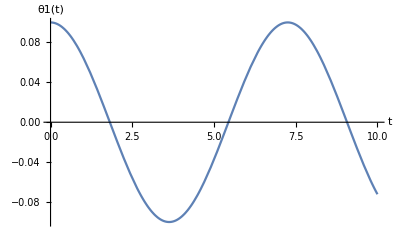

```mathematica
Plot[ Evaluate[ q[[1]] /. solution[t] ]   , { t, 0, 10 } , AxesLabel-> { t, q[[1]] }   ]
```

```mathematica
Animate[
ParametricPlot[ { solution[t][[1,2]] , solution'[t][[1,2]] } , { t, 0, tmax } , AxesLabel-> { q[[1]] , D[q[[1]], t] } ]  , { tmax , 0.1 , 20 } ]
```

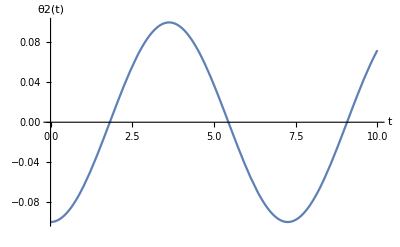

```mathematica
Plot[ Evaluate[ q[[2]] /. solution[t] ]   , { t, 0, 10 } , AxesLabel-> { t, q[[2]] }   ]
```

```mathematica
Animate[
ParametricPlot[ { solution[t][[2,2]] , solution'[t][[2,2]] } , { t, 0, tmax }  , 
AxesLabel-> { q[[2]] , D[q[[2]], t] }]  , { tmax , 0.1 , 20 } ]
```